```mathematica
SetDirectory[NotebookDirectory[]];
<<preamble.m
<<Geodesics.m
<<VorticityGeneration.m
```

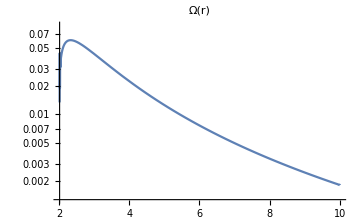
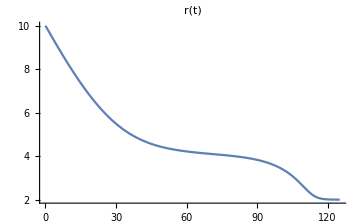
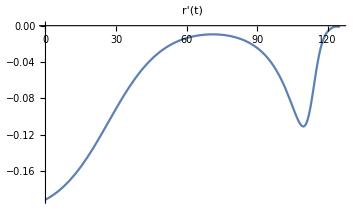
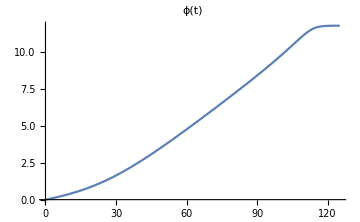
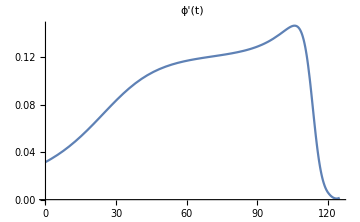
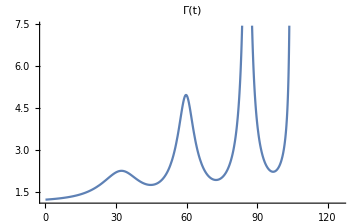
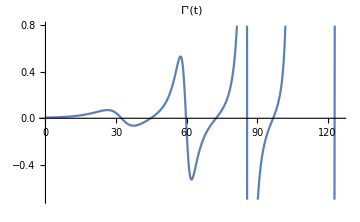
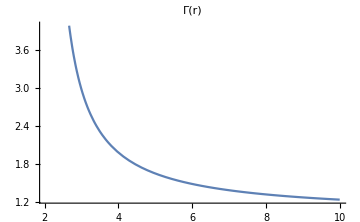
-Graphics- | 
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[{
{LogPlot[Ω[r],{r,rmin,rmax},PlotLabel->"Ω(r)",ImageSize->Medium],Animate[Show[ParametricPlot[{Re[r[τ]]Re[Cos[ϕ[τ]]],Re[r[τ]]Re[Sin[ϕ[τ]]]}/.sol[[solnumber]],{τ,τmin,time},PlotRange->rmax,PlotLabel->"Geodesic",ImageSize->Medium],BHplot],{time,τmax/10,τmax}]},
{Plot[roft[t],{t,tmin,tmax},PlotLabel->"r(t)",ImageSize->Medium],
Plot[roft'[t],{t,tmin,tmax},PlotLabel->"r'(t)",ImageSize->Medium]},
{Plot[ϕoft[t],{t,tmin,tmax},PlotLabel->"ϕ(t)",ImageSize->Medium],
Plot[ϕoft'[t],{t,tmin,tmax},PlotLabel->"ϕ'(t)",ImageSize->Medium]},
{Plot[Γoft[t],{t,tmin,tmax},PlotLabel->"Γ(t)",ImageSize->Medium],
Plot[Γoft'[t],{t,tmin,tmax},PlotLabel->"Γ'(t)",ImageSize->Medium]},
{Plot[Γofr1[r],{r,rmin,rmax},PlotLabel->"Γ(r)",ImageSize->Medium],
Plot[Γofr1'[r],{r,rmin,rmax},PlotLabel->"Γ'(r)",ImageSize->Medium]}
},Frame->All]
```